```mathematica
paramvals={v->1,dstep->8,fs->5,w->2,fd->4,a->1.07,b->.186,ϵ0->.7};
```

## Stepping rate

rate from my definition

```mathematica
kstep[f_]:=Piecewise[{{v/dstep (1-(f/fs)^w),0<f<fs},{0,f≥fs},{v/dstep,f<0}}]
```

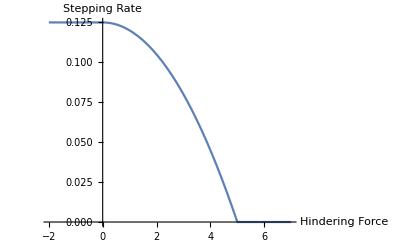

```mathematica
Plot[kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force","Stepping Rate"}]
```

translate to velocity

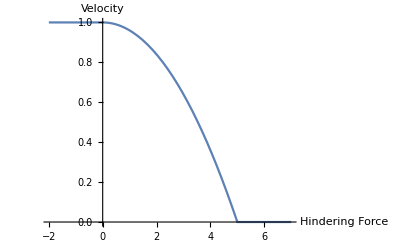

```mathematica
Plot[dstep*kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force","Velocity"}]
```

## Run Length

My off rate

```mathematica
koff[f_]:=Piecewise[{{ϵ0 Exp[Abs[f]/fd],f≤fd},{a+b f,f>fd}}]
```

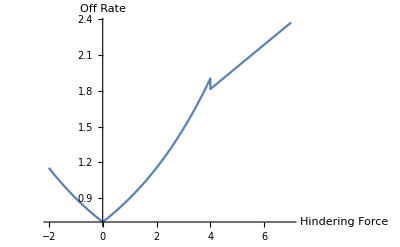

```mathematica
Plot[koff[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force","Off Rate"}]
```

Then my run length is

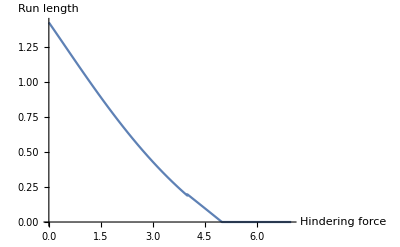

```mathematica
Plot[(dstep kstep[f])/koff[f]/.paramvals,{f,0,7},AxesLabel->{"Hindering force","Run length"}]
```

So, it’s about exponential